```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}];
```

```mathematica
Cascade3[z_, r_]= Normal[Series[Ggauss[q, z, r]-q, {q, 0,3}]];
```

```mathematica
Cascade[z_, r_] = SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,1}],1];
```

```mathematica
Cascade2[z_, r_] = (SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],0]*SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,2}],2]);
```

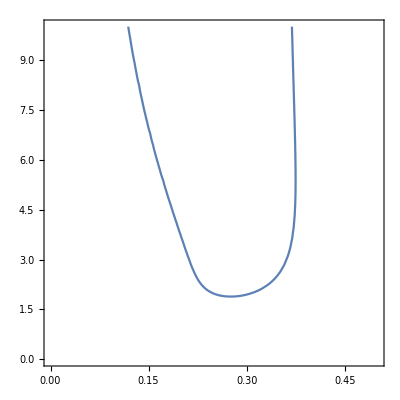

```mathematica
ContourPlot[(Cascade2[z, r])==0, {r, 0, 0.5}, {z,0,10}, ContourStyle->"dashed"]
```

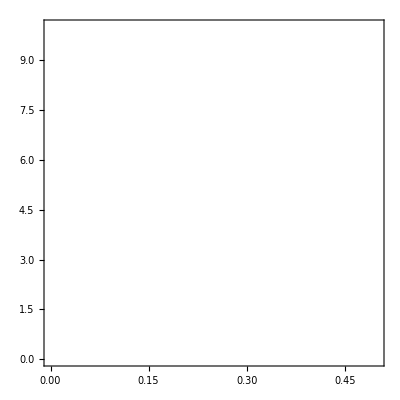

```mathematica
ContourPlot[Cascade2[z,r]==0,{r,0,0.5},{z,0,10},ContourStyle->Directive[RGBColor[1.,1.,1.],Opacity[0.4]]]
```

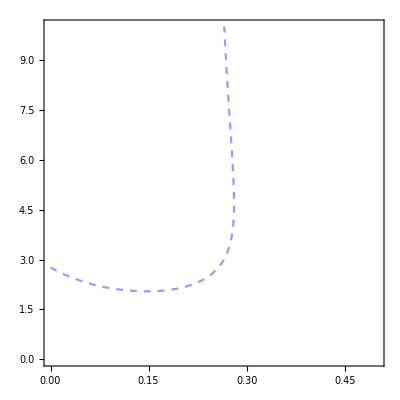

```mathematica
ContourPlot[Cascade[z,r]-1==0,{r,0,0.5},{z,0,10},ContourStyle->Directive[RGBColor[0.,0.,1.],Opacity[0.4],Dashed]]
```

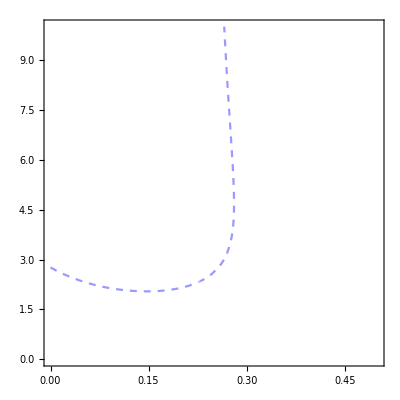

```mathematica
Show[%8, %26]
```

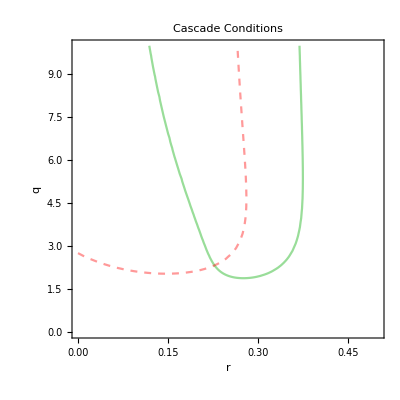

```mathematica
Show[%12,FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[Cascade Conditions],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/single_layer_cascade.eps",%13,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/single_layer_cascade.eps

```mathematica
data=BinaryReadList["/home/user/Documents/BT_MP/BT_MP/coordination_game/simulations/pp_node_swap_sim_100_com.dat","Real32"];
```

```mathematica
griddat = ArrayReshape[data, {20, 21}];
```

```mathematica
zcoord = Range[0.5, 10, 0.5];
```

```mathematica
rcoord = Range[0, 0.4, 0.02];
```

```mathematica
Flatten[Table[{rcoord[[j]],zcoord[[i]],griddat[[i,j]]},{j,21},{i,20}],1];
```

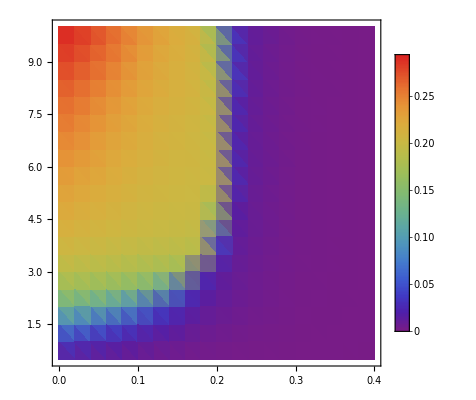

```mathematica
ListDensityPlot[%%, ColorFunction->"Rainbow", PlotLegends->Automatic]
```

```mathematica
GN1gauss[q_, p_, z_, r_] = (Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}])* (Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]);
```

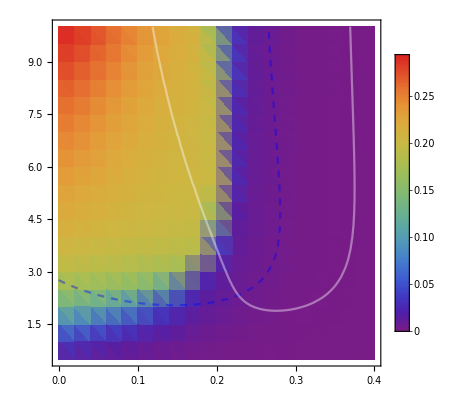

```mathematica
Show[%93, %27]
```

```mathematica
data
```

{0.0110867,0.00901333,0.00728,0.00618,0.00500667,0.00424667,0.00294667,0.00264667,0.00178667,0.00122,0.00124667,0.000746667,0.000566667,0.000473333,0.000326667,0.000146667,0.0001,0.0000866667,0.0000666667,0.0000733333,0.0000466667,0.03932,0.0318133,0.0259333,0.0219133,0.0171933,0.0140467,0.0100067,0.00858,0.00604,0.00427333,0.00316,0.00218,0.00158667,0.00134667,0.00092,0.000513333,0.000346667,0.00022,0.00016,0.000146667,0.0000866667,0.0844533,0.07508,0.0657067,0.05232,0.04156,0.03248,0.0220133,0.01802,0.0113333,0.00775333,0.00633333,0.00434,0.00289333,0.00212667,0.00152,0.000986667,0.000493333,0.000506667,0.00026,0.000166667,0.0000933333,0.133473,0.126213,0.118947,0.111507,0.0954267,0.07968,0.0468333,0.03276,0.0208933,0.01182,0.00836667,0.00614,0.00405333,0.00306667,0.00190667,0.000906667,0.00058,0.000566667,0.000433333,0.000246667,0.000113333,0.167713,0.165127,0.161987,0.157807,0.152667,0.146747,0.132653,0.0970733,0.0368,0.0190667,0.0119533,0.00764,0.00523333,0.00372667,0.00222,0.00126,0.000893333,0.000653333,0.000453333,0.0003,0.000133333,0.18872,0.18716,0.18476,0.18272,0.18032,0.177213,0.173467,0.170327,0.164173,0.0320333,0.01342,0.00892,0.00558667,0.00448667,0.00272,0.00125333,0.00096,0.000686667,0.00048,0.00034,0.000166667,0.202667,0.199707,0.19816,0.195767,0.194193,0.191673,0.190147,0.188333,0.18702,0.181627,0.0304933,0.0105733,0.00665333,0.00438667,0.00293333,0.00162,0.00110667,0.00074,0.000453333,0.00036,0.00014,0.212393,0.210233,0.206953,0.204427,0.202253,0.199673,0.19782,0.19636,0.19528,0.1936,0.0537,0.01204,0.00693333,0.00493333,0.00296667,0.00164667,0.00122,0.000773333,0.000553333,0.00038,0.00016,0.21922,0.21576,0.212633,0.209893,0.207467,0.20478,0.2026,0.200573,0.199733,0.198413,0.152287,0.0151667,0.00828667,0.00598667,0.00308667,0.00173333,0.00104,0.000826667,0.000553333,0.00038,0.000193333,0.225607,0.222067,0.21884,0.21506,0.211687,0.207633,0.205587,0.20344,0.202233,0.201033,0.17532,0.0189867,0.00757333,0.00545333,0.00345333,0.00185333,0.00111333,0.000853333,0.00054,0.000393333,0.000153333,0.231667,0.22644,0.22294,0.218713,0.215047,0.21094,0.207927,0.205153,0.203727,0.202813,0.199633,0.0303267,0.00916,0.00596,0.00348667,0.00172667,0.00112,0.0009,0.000566667,0.0004,0.000186667,0.2396,0.233007,0.23008,0.2231,0.219207,0.213413,0.210853,0.207033,0.20572,0.204007,0.19642,0.0267867,0.00945333,0.00672,0.00378667,0.00186667,0.00114667,0.00086,0.00054,0.000393333,0.000193333,0.244787,0.239547,0.234407,0.22654,0.2216,0.21726,0.213027,0.20788,0.207227,0.20324,0.197267,0.0279933,0.00891333,0.00584,0.00366667,0.00187333,0.00121333,0.000826667,0.000613333,0.000433333,0.000166667,0.250033,0.247533,0.238487,0.231687,0.226147,0.21898,0.21478,0.210313,0.20754,0.203753,0.193853,0.02628,0.00980667,0.00694667,0.00373333,0.00206667,0.00132667,0.000853333,0.00058,0.00038,0.0002,0.2587,0.2522,0.245847,0.235253,0.229833,0.22212,0.217127,0.211993,0.20864,0.205093,0.195607,0.0296867,0.00904667,0.0062,0.0037,0.00183333,0.00130667,0.000906667,0.000593333,0.000386667,0.000193333,0.263107,0.259927,0.25126,0.241773,0.234653,0.225373,0.220987,0.214167,0.211913,0.20762,0.188627,0.0268333,0.01056,0.0066,0.00376667,0.00183333,0.00127333,0.000846667,0.000646667,0.000406667,0.00018,0.273067,0.265807,0.25928,0.248873,0.240193,0.228867,0.223233,0.21598,0.212873,0.20442,0.186813,0.0402467,0.0107267,0.00672,0.00408,0.00204667,0.00129333,0.001,0.000633333,0.00042,0.000186667,0.28028,0.274347,0.266287,0.256687,0.247767,0.233253,0.226713,0.217353,0.214567,0.207333,0.17686,0.0400333,0.0117867,0.00693333,0.00415333,0.0021,0.00135333,0.000866667,0.000626667,0.00044,0.000186667,0.287993,0.282853,0.272587,0.261873,0.25238,0.239307,0.229627,0.221133,0.214707,0.20812,0.165927,0.0399867,0.00987333,0.00737333,0.00423333,0.00214667,0.00119333,0.00100667,0.000666667,0.00042,0.000193333,0.293973,0.28792,0.279913,0.266527,0.25716,0.243273,0.23272,0.221893,0.216907,0.203853,0.163133,0.03702,0.0116267,0.00898667,0.00442667,0.00208667,0.00134,0.000973333,0.000606667,0.000393333,0.00022}

```mathematica
%37
```

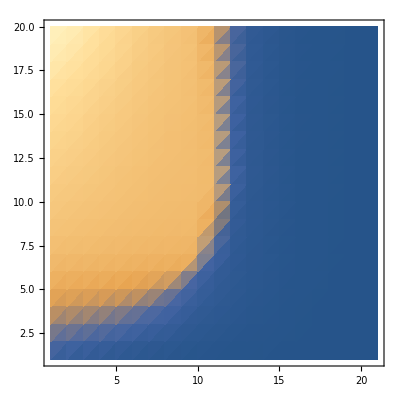

```mathematica
ListDensityPlot[griddat]
```